# 2.1 Degenerate System

## a) Plot the trajectories for sigma = {-1,0,1}

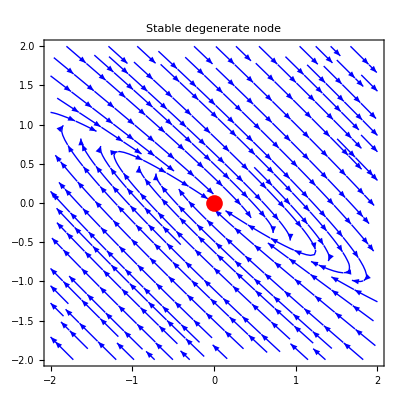

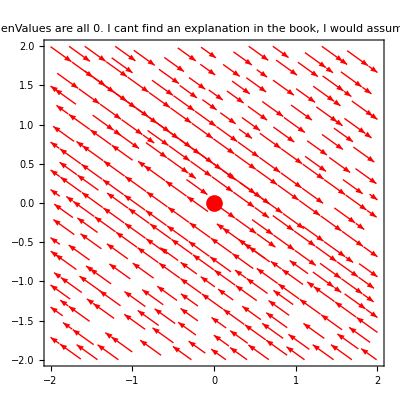

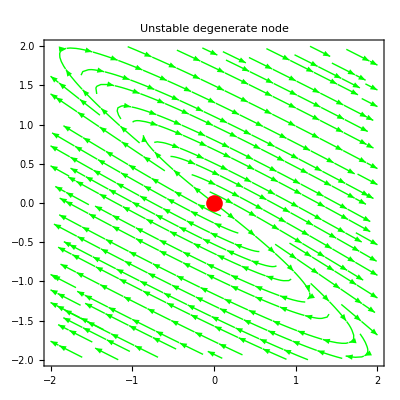

```mathematica
(*sigma = -1*)
sigma = -1;
p1=StreamPlot[{(sigma + 3)*x +4*y , -(9/4)*x + (sigma-3)y},{x,-2,2},{y,-2,2},
StreamColorFunction->None , StreamStyle->Blue, PlotLabel->"Stable degenerate node", Epilog->{Red, PointSize[0.03], Point[{0,0}]}]
sigma = 0;
p2=StreamPlot[{(sigma + 3)*x +4*y , -(9/4)*x + (sigma-3)y},{x,-2,2},{y,-2,2},
StreamColorFunction->None , StreamStyle->Red, PlotLabel->"Not isolated fixed points -> Det / Trace / EigenValues are all 0. \n I cant find an explanation in the book, I would assume there is a \nline of unstable fixed points on y=-x", Epilog->{Red, PointSize[0.03], Point[{0,0}]}]
sigma = 1;
p3=StreamPlot[{(sigma + 3)*x +4*y , -(9/4)*x + (sigma-3)y},{x,-2,2},{y,-2,2},
StreamColorFunction->None , StreamStyle->Green, PlotLabel->"Unstable degenerate node", Epilog->{Red, PointSize[0.03], Point[{0,0}]}]
```

To determine the stability, check the determinant of A

```mathematica
ClearAll["Global`*"]
Clear[sigma]
A={{(sigma+3),4},{-(9/4),sigma-3}};
det = Det[A]//Simplify
trac = sigma + 3 + sigma -3
Parabola = trac^2 - 4 * det
```

sigma^2

2 sigma

0

One sees that for all values of σ the equation of the parabola = 0. Therefore we always move on that parabola and have a stable σ<0, an unstable degenerate node σ>0 and a center for σ=0. The signs of the the eigenvalues λ determine if the flow is going inwards the stable point or outwards
-Graphics-;

## b) -> eigVal of A

```mathematica
Clear[sigma];(*Clears any previous definition of sigma*)
A={{(sigma+3),4},{-(9/4),sigma-3}}
Eigenvalues[A]//Simplify
```

{{3+sigma,4},{-9/4,-3+sigma}}

{sigma,sigma}

## c) -> eigVec of A

```mathematica
Eigenvectors[A]
```

{{-4/3,1},{0,0}}

```mathematica
{{-4/3,1},{0,0}}
(*Rewrite by hand to norm -> other PDF*)
eigV = {-4/3,1};
n = Norm[eigV];
solC = (-1)*eigV/n
```

{{-4/3,1},{0,0}}

{4/5,-3/5}

## d) -> A^-1

```mathematica
A_inv = Inverse[A]//MatrixForm // Simplify
```

((-3+sigma)/sigma^2 | -4/sigma^2
9/(4 sigma^2) | (3+sigma)/sigma^2)

## e) -> for which sigma is A singular -> det == 0

```mathematica
Clear[sigma]
A={{(sigma+3),4},{-(9/4),sigma-3}}
sigma_star = Solve[Det[A]==0, sigma]
```

{{3+sigma,4},{-9/4,-3+sigma}}

{{sigma→0},{sigma→0}}

## f) find the direction of the line o the fixed points

```mathematica
B[sigma_] = {{sigma -c*d, d^2},{-c^2,sigma+c*d}}
```

{{-c d+sigma,d^2},{-c^2,c d+sigma}}

```mathematica
{{-c d+sigma,d^2},{-c^2,c d+sigma}}
sol1  = Eigenvectors[B[0]]
norm = Norm[sol1[[0]]]
```

{{-c d+sigma,d^2},{-c^2,c d+sigma}}

{{d/c,1},{0,0}}

Norm[List]

```mathematica
{{d/c,1},{0,0}}
eigVec = {d/c,1}
```

{{d/c,1},{0,0}}

{d/c,1}

```mathematica
n = Norm[eigVec]
```

√(1+Abs[d/c]^2)

```mathematica
√(1+Abs[d/c]^2)
eigVec/n//Simplify
```

√(1+Abs[d/c]^2)

{d/(c √(1+Abs[d/c]^2)),1/(√(1+Abs[d/c]^2))}